```mathematica
Quit[];
```

```mathematica
<<FeynCalc`
```

FeynCalc 9.3.0 (development version). For help, use the documentation center, check out the wiki or write to the mailing list.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

```mathematica
FCClearScalarProducts[]
```

```mathematica
M = -ⅈ*e*Subscript[g, sbb] Subscript[c, w] Subscript[s, w] SpinorU[Subscript[k, 1],Subscript[m, e]].GA[μ].SpinorVBar[Subscript[k, 2], Subscript[m, e]](-MT[μ,ν] + FV[Subscript[k, 1]+Subscript[k, 2],μ]FV[Subscript[k, 1]+Subscript[k, 2],ν])/(SP[Subscript[k, 1]+Subscript[k, 2],Subscript[k, 1]+Subscript[k, 2]] - Subscript[m, z]^2+ⅈ*Subscript[m, z]*Subscript[Γ, z])(-FV[Subscript[p, 2],ν]FV[Subscript[k, 1]+Subscript[k, 2],ρ]+SP[Subscript[k, 1]+Subscript[k, 2],Subscript[p, 2]]MT[ν,ρ])PolarizationVector[Subscript[p, 2],ρ,Transversality->True]
```

-(ⅈ e c_w g_sbb s_w (ε̄)^ρ(p_2) (((k̄)_1+(k̄)_2)^μ ((k̄)_1+(k̄)_2)^ν-(ḡ)^μν) u(k_1,m_e).(γ̄)^μ.v̄(k_2,m_e) ((ḡ)^νρ (((k̄)_1+(k̄)_2)·(p̄)_2)-((k̄)_1+(k̄)_2)^ρ ((p̄)_2)^ν))/(((k̄)_1+(k̄)_2)^2+ⅈ m_z Γ_z-m_z^2)

```mathematica
M1 = M//Contract//Simplify;
```

```mathematica
SP[Subscript[k, 1],Subscript[k, 1]] = Subscript[m, e]^2;
SP[Subscript[k, 2],Subscript[k, 2]] = Subscript[m, e]^2;
SP[Subscript[k, 1],Subscript[k, 2]] = Subscript[m, z]^2/2;
SP[Subscript[p, 2],Subscript[p, 2]] = 0;
SP[Subscript[p, 1],Subscript[p, 1]] = Subscript[m, ϕ]^2;
E2 = (Subscript[m, z]^2 - Subscript[m, ϕ]^2)/(2 Subscript[m, z]);
SP[Subscript[k, 1],Subscript[p, 2]] = E2*Subscript[m, z]/2(1 - Cos[θ]);
SP[Subscript[k, 2],Subscript[p, 2]] = E2*Subscript[m, z]/2(1 + Cos[θ]);
```

```mathematica
ampSquared[0] = Simplify[
DiracSimplify[
(FermionSpinSum[#1, ExtraFactor-> 1/2^2] & ) [
(DoPolarizationSums[#1, Subscript[p, 2], 0] & ) [
FeynAmpDenominatorExplicit[M1 *ComplexConjugate[M1]
]
]
]
]
]
```

(e^2 c_w^2 g_sbb^2 s_w^2 ((4 m_e^2+m_z^2) ((k̄)_1·(p̄)_2)^2+(4 m_e^2+m_z^2) ((k̄)_2·(p̄)_2)^2+4 m_e^2 ((k̄)_2·(p̄)_2) ((k̄)_1·(p̄)_2)))/(4 m_e^4+m_z^2 Γ_z^2)

```mathematica
ampSquared[1] = ampSquared[0]/.Subscript[m, e]-> 0//Simplify
```

(e^2 c_w^2 g_sbb^2 (cos(2 θ)+3) s_w^2 (m_z^2-m_ϕ^2)^2)/(16 Γ_z^2)

```mathematica
diffsig = ampSquared[1]/(64 π^2 Subscript[m, z]^2)*2/Subscript[m, z]*E2//Simplify
```

(e^2 c_w^2 g_sbb^2 (cos(2 θ)+3) s_w^2 (m_z^2-m_ϕ^2)^3)/(1024 π^2 m_z^4 Γ_z^2)

```mathematica
sig = Integrate[2*π*diffsig*Sin[θ],{θ,0,π}]//Simplify;
```

```mathematica
numerical = sig*(.389*10^-3)/10^-12/.e-> .303/.Subscript[s, w]-> Sqrt[.23120]/.Subscript[c, w]-> Sqrt[1 - .23120]/.Subscript[Γ, z]-> 2.5/.Subscript[m, z]-> 91.18/.Subscript[g, sbb]-> 10^-3;
```

```mathematica
num[mass_]:= numerical/.Subscript[m, ϕ]-> mass;
```

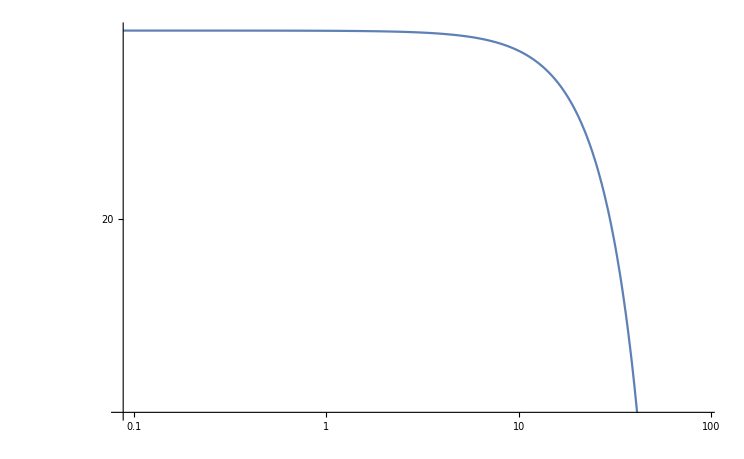

```mathematica
LogLogPlot[num[m], {m, 0, 90}]
```

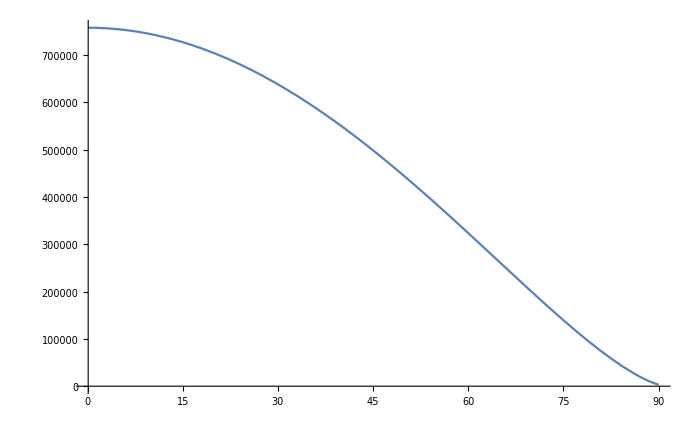

```mathematica
Plot[(91.18^2 - m^2)^1.5, {m, 0.1, 90}]
```

```mathematica
2/(89.91*10^-3)
```

22.2445

```mathematica
%/10^-3
```

22244.5

```mathematica
sigmaZ = 22244.5;
```

```mathematica
Γzphia = g^2 sw^2 cw^2((Subscript[m, z]^2 - Subscript[m, ϕ]^2)^3)/(96π*Subscript[m, z]^3);
```

```mathematica
sigapp = 22244.5*(g^2 sw^2 cw^2((Subscript[m, z]^2 - Subscript[m, ϕ]^2)^3)/(96π*Subscript[m, z]^3))/Subscript[Γ, Z];
```

```mathematica
sigapprox= sigapp/.g-> 10^-3/.sw->Sqrt[.23120]/.cw-> Sqrt[1 - .23120]/.Subscript[Γ, Z]-> 2.5 /.Subscript[m, z]-> 91.18/.Subscript[m, ϕ]-> 0.5
```

3.97486

```mathematica
sigapprox[20]
```

3.8335(20)

```mathematica
sigapprox[10]
```

(73.7567 cw^2 g^2 sw^2 (m_z^2-m_ϕ^2)^3)/(m_z^3 Γ_Z)(10)